# Calculating AVS Curves

## QEA Boats Module

By Dieter Brehm & Sam Sam Daitzman

## Explanation

### This file contains Mathematica code for calculating the RM curve of a differently shaped three dimensional boats. First, we define our desired boats. Then, we define a function for finding the moment at a given heal angle. Finally, we map that function to several angles and generate a plot.

## Code

Defining and showing a plot of the two boats

```mathematica
oldboat = ImplicitRegion[x^2/2<y<2 && -2 < x<2&&0<y<2 && -5 < z <5, {x,y,z}]
```

ImplicitRegion[x^2/2<y<2&&-2<x<2&&0<y<2&&-5<z<5,{x,y,z}]

```mathematica
RegionPlot3D[oldboat, PlotTheme->"Web", AxesLabel->{"y","x","z"}, PlotPoints->55, PlotStyle->Directive[Yellow,Opacity[0.5]]]
```

-Graphics3D-

```mathematica
boat = ImplicitRegion[x^2/2^2+y^2/2^2 +z^2/4^2<1 ,{ {x,-2,2},{y,-2,0},{z,-4,4}}];
```

```mathematica
Show[
RegionPlot3D[boat, PlotTheme->"Web", AxesLabel->{"y","x","z"}, PlotPoints->55, PlotStyle->Directive[Yellow,Opacity[0.5]]],
ListPointPlot3D[{{0,-0.5008819219921405,0}}, PlotStyle->Directive[Cyan,Opacity[1]]]]
```

-Graphics3D-

Code for calculating moment of arbitrary ImplicitRegion boat at a heel angle

```mathematica
boatmass[boatregion_, density_] :=
 mass = N[(Volume[boatregion]*300)+5000,5]
boatcom[boatregion_, density_] := 
com = N[ 1/boatmass[boatregion, density]*NIntegrate[300*{x,y,z}, {x,y,z}∈boatregion],5]
moment[hullshape_,mass_,com_,density_, theta_]:= Module[{},
rads = theta * (Pi/180);
water = ImplicitRegion[If[rads<Pi / 2,y<Tan[rads ]*x+d,y>Tan[rads]*x+d],{{x,-2,2},{y,-2,2}, {z,-5,5}}];
under = RegionIntersection[hullshape, water];
disp = Integrate[1000, {x,y,z}∈under];
WriteString[$Output,"Hello solver!\n"];
draft = N[d/.FindRoot[disp==mass,{d,-20,20}][[1]]];
cob = RegionCentroid[under/.{d->draft}];
buoyancy = mass*98/10*{-Sin[rads],Cos[rads],0};
torque =Cross[cob-com, buoyancy][[3]];
torque]
```

```mathematica
moment[oldboat,boatmass[oldboat, 300.],boatcom[oldboat,300.],300.,30.]
```

Testing intermediary functions and plots

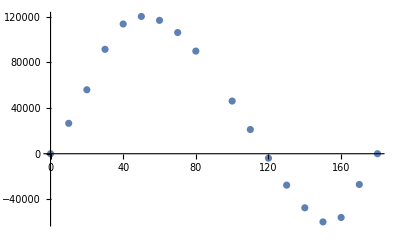

```mathematica
ListPlot[Table[{theta,moment[oldboat,boatmass[oldboat, 300],boatcom[oldboat,300],300,theta]},{theta,{0,10,20,30,40,50,60,70,80,100,110,120,130,140,150,160,170,180}}]]
```

Attempted mapping of angles to moment outputs

I can’t seem to get this to run reasonably. It takes much longer for this to run (I havn’t run it long enough for it to finish because it is taking so long} than just manually running the function and entering plot points.

```mathematica
(*data =Table[{theta,moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,theta]},{theta,{0.,10.,20.,30.,40.,50.,60.,70.,80.,100.,110.,120.,130.,140.,150.,160.,170.,180.}}]*)
```

```mathematica
boatmass[boat, 300.]
boatcom[boat,300.]
```

15053.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{0.,-0.500882,0.}

```mathematica
f[anAngle_] := (
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,anAngle])
rmcurve[boat_] := (Quiet[Parallelize[Table[{angle,N[f[angle]]},{angle,1,179,179}]]])
findAVS[boat_]:= (
f = Interpolation[rmcurve[boat]];
FindRoot[f[x]==0,{x,100}])
PlotAVS[boat_]:=(
curves = rmcurve[boat];
f = Interpolation[curves];
Show[ListPlot[curves],Plot[f[x],{x,1,179}]])
findAVS[boat]
```

Hello World!

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

$Aborted

```mathematica
findavsfunc[anAngle_] := moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,anAngle]
```

```mathematica
angleTable=Quiet[Parallelize[Table[{angle,N[ findavsfunc[angle],5]},{angle,1,179,10}]]]
```

```mathematica
ListPlot[angleTable]
```

-Graphics-

manual runs of data for ellipse boat

```mathematica
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,10.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,20.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,30.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,40.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,50.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,60.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,70.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,80.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,100.]
moment[boat,boatmass[boat, 300.],boatcom[boat,300.],300.,120.]
```

```mathematica
exampledata={{10,12830},{20,25272},{30,34154},{40,32391},{50,23743},{60,11126},{70,-3683},{80,-19432},{100,-49838},{120,-73074}}
```

{{10,12830},{20,25272},{30,34154},{40,32391},{50,23743},{60,11126},{70,-3683},{80,-19432},{100,-49838},{120,-73074}}

```mathematica
f = Interpolation[exampledata]
```

InterpolatingFunction[…]

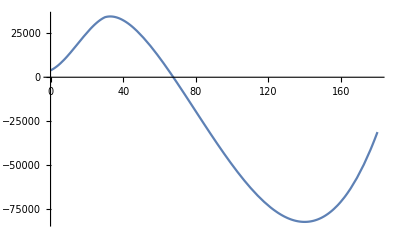

```mathematica
Plot[f[x],{x,0,180}]
```

```mathematica
FindRoot[f[x]==0,{x,100}]
```

{x→67.6027}